# 1. Wczytanie plików

```mathematica
path="/home/michaszko/Documents/Neutrina/Opus/MINERvA_anu";
type="LFG";
scalingFactor=10^41;
mecDim=24;
eventsNumber=10^6;
crossSection=8.65493*10^-40;

Subscript[Δp, T]={150,100,150,300,300,500};
Subscript[Δp, L]={500,500,500,500,500,1000,1000,2000,2000,5000};
dpT={0,150,250,400,700,1000};
dpL={1500,2000,2500,3000,3500,4000,5000,6000,8000,10000,15000};
widthVanilla=Flatten[KroneckerProduct[Subscript[Δp, T],Subscript[Δp, L]]];

lenPT=Length[Subscript[Δp, T]];
lenPL=Length[Subscript[Δp, L]];

(*******************************)

matVanilla=Import[path<>"/Data/matrix_"<>type<>".dat"];
mecVanillaMatrix=Import[path<>"/Data/cros_mec_nuwro_"<>type<>".dat"];
totalVanillaMatrix=Import[path<>"/Data/cros_total_nuwro_"<>type<>".dat"];
danielVanillaMatrix=Import[path<>"/Data/cros_total_daniel.dat"];
covNonVanilla=Import[path<>"/Data/daniel_covariance_vanilla.dat"];

(*****************************************)

matVanilla=matVanilla/eventsNumber*crossSection*1000000/widthVanilla*12/13*scalingFactor;

mecVanilla=Flatten[Transpose[mecVanillaMatrix]]*scalingFactor;
totalVanilla=Flatten[Transpose[totalVanillaMatrix]]*scalingFactor;
danielVanilla=Flatten[danielVanillaMatrix];

rozVanilla=(danielVanilla-totalVanilla+mecVanilla)(*/.(y_/;y<0)->0*);

covVanilla=PseudoInverse[covNonVanilla];
errorVanilla=Sqrt[Diagonal[covNonVanilla]];
errorVanillaError = errorVanilla/.(y_/;y==0)->10^40;

(**********************************************)

MatrixPlot[matVanilla];

(**************************************************)

BarChart[Partition[Plus@@Transpose[matVanilla],lenPL][[#]],GridLines->Automatic,BarSpacing->None,ImageSize->Large,PlotLabel->(#-1)]&/@Range[lenPT];

MatrixPlot[Partition[Plus@@matVanilla,mecDim],DataReversed->True,PlotLegends->Automatic];

Plus@@Transpose[matVanilla]-mecVanilla//ListPlot;
```

# 2. Test

## χ^2 bez kowariancji

```mathematica
newVanilla=matVanilla.ConstantArray[1,mecDim^2];
(*errorVanillaError = errorVanilla/.(y_/;y==0)->1;*)


x=(danielVanilla-totalVanilla+mecVanilla-newVanilla)^2/errorVanillaError^2;
Plus@@Transpose[Partition[x,10]];
MatrixForm[Partition[x,10]];
MatrixPlot[Partition[x,10],PlotLegends->Automatic];
χ=Plus@@x
```

112.081

## χ^2 z kowariancją

```mathematica
newVanilla=matVanilla.ConstantArray[1,mecDim^2];
(newVanilla-Plus@@Transpose[matVanilla])*10^40;
(newVanilla-mecVanilla)*10^40;
(danielVanilla-totalVanilla+mecVanilla-newVanilla).covVanilla.(danielVanilla-totalVanilla+mecVanilla-newVanilla)
(rozVanilla-newVanilla).covVanilla.(rozVanilla-newVanilla)
```

72.4326

72.4326

## Dodatki do χ^2 z kowariancją

```mathematica
Partition[(danielVanilla-totalVanilla+mecVanilla-newVanilla)*covVanilla.(danielVanilla-totalVanilla+mecVanilla-newVanilla),12];
MatrixPlot[%,PlotLegends->Automatic];
MatrixForm@%%;
```

## Test macierzy kowaricanji

```mathematica
MatrixPlot[Partition[(Diagonal[covNonVanilla]/(1/errorVanillaError^2))/.(y_/;y>100 || y<-100)->1,12],PlotLegends->Automatic];
Histogram[(Diagonal[covNonVanilla]/(1/errorVanillaError^2))/.(y_/;y>100 || y<-100)->0];
Clear[chi2cov]
covNonVanilla.covVanilla//Chop//MatrixForm;
(Diagonal[covNonVanilla]-errorVanillaError^2)*10^80;
```

# 3. Rozwiązanie

```mathematica
emptyValue=0.3;

V=Table[Subscript[v, i,j],{i,1,mecDim},{j,1,mecDim}]//Flatten ;
V1=Table[Subscript[v, i,j],{i,1,mecDim},{j,i,mecDim}]//Flatten;
V2=Table[Subscript[v, i,j],{i,2,mecDim},{j,1,i-1}]//Flatten;
V3=V/.Thread[V2->emptyValue];

chi2[x_]:=Plus@@((rozVanilla-matVanilla.x)/errorVanillaError)

chi2cov[x_]:=(rozVanilla-matVanilla.x).covVanilla.(rozVanilla-matVanilla.x)

plotMec[x_,fun_]:=MatrixPlot[
Partition[x,mecDim],
PlotLegends->Automatic,
DataReversed->True,
PlotLabel->{"χ^2 = "<> ToString[fun[x]]}]


condition=Module[{a,p},
p=0.5;
a=Join[
Thread[V1≥ 0],
(*Thread[Subscript[V, 2]==1],*)
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i,j-1])/(Subscript[v, i,j]+Subscript[v, i,j-1])]<p,{i,1,mecDim},{j,2,mecDim}]],
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i,j+1])/(Subscript[v, i,j]+Subscript[v, i,j+1])]<p,{i,1,mecDim},{j,1,mecDim-1}]],
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i-1,j])/(Subscript[v, i,j]+Subscript[v, i-1,j])]<p,{i,2,mecDim},{j,1,mecDim}]],
Flatten[Table[Abs[(Subscript[v, i,j]-Subscript[v, i+1,j])/(Subscript[v, i,j]+Subscript[v, i+1,j])]<p,{i,1,mecDim-1},{j,1,mecDim}]]];And@@DeleteDuplicates[a/.Thread[V2->emptyValue]]];

minChi2[fun_,iter_:100,acura_:Automatic,prec_:Automatic]:=
NMinimize[
{fun[V3],condition},
V1,
MaxIterations->iter,
AccuracyGoal->acura,
PrecisionGoal->prec,
Method->"RandomSearch",
StepMonitor:>(
Export[path<>"/chi2Values/"<>ToString[fun]<>"_"<>ToString[Round[fun[V3]]]<>".dat",Partition[V3,mecDim]];Print[plotMec[V3/emptyValue->1,fun]])];
```

## χ^2 bez kowariancji

```mathematica
{chi2Value,chi2Solution}=minChi2[chi2,2];
```

```mathematica
tmp=Import[path<>"/chi2Values/chi2_232.dat"];
MatrixPlot[tmp/.{0.3->0},DataReversed->True,PlotLegends->Automatic,PlotLabel->chi2[Flatten@tmp]]
```

## χ^2 z kowariancją

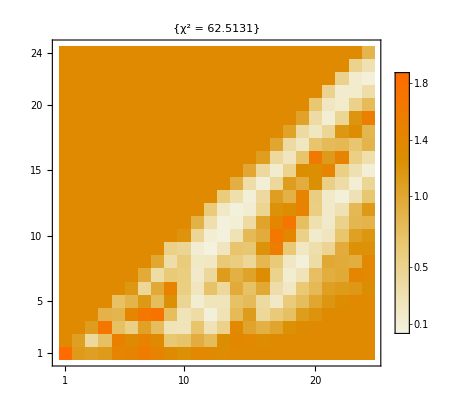

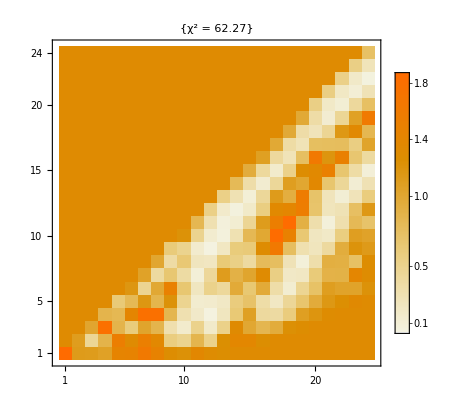

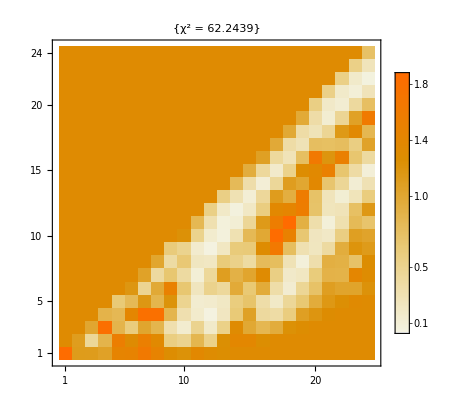

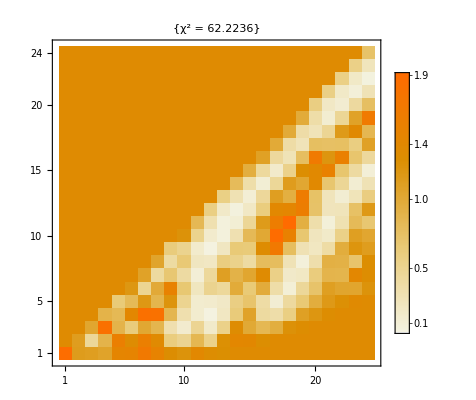

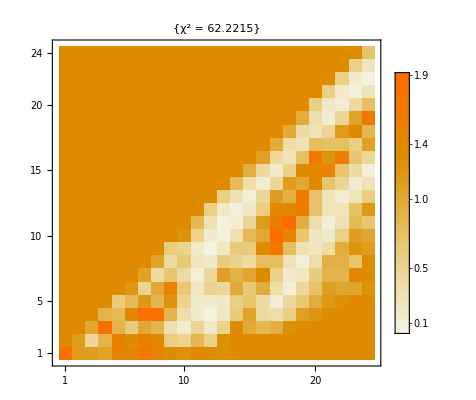

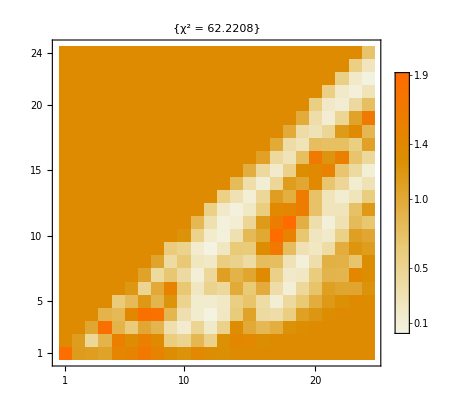

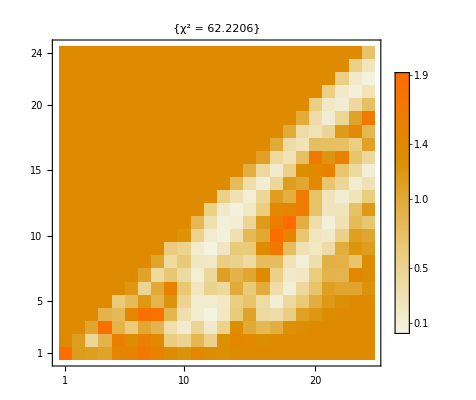

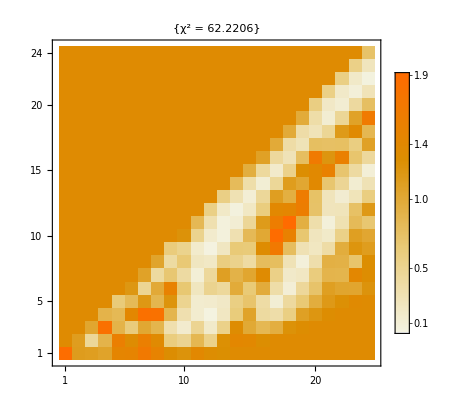

-Graphics-

-Graphics-

-Graphics-

-Graphics-

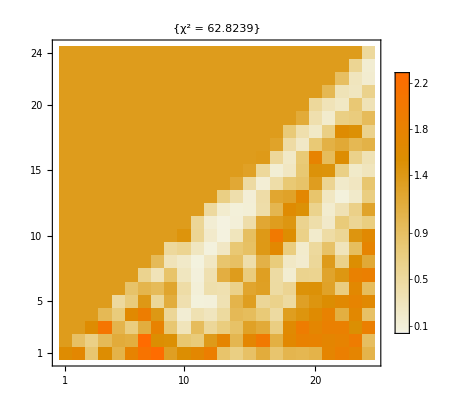

$Aborted

```mathematica
{chi2CovValue,chi2CovSolution}=minChi2[chi2cov]
```

```mathematica
tmp=Import[path<>"/chi2Values/chi2cov_63.dat"];

(*ArrayPlot[
tmp,
DataReversed->True,
PlotLabel->"χ^2 = "<>ToString@chi2cov[Flatten@temp],
AxesLabel->{ω,q},
PlotLegends->Automatic,
ColorFunction->"TemperatureMap",
FrameTicks->All,
PlotRange->1.2]*)
```

# asmfsa

```mathematica
a=RectangleChart[
Thread[{Subscript[Δp, T],Take[totalVanilla,{#,-1,lenPL}]}],
GridLines->Automatic,
BarSpacing->None,
(*ImageSize->Full,*)
ChartStyle->Yellow,
PlotLabel->"CC 0π ν_μ, NuWro before rescaling, " <> ToString[dpL[[#]]]<>" < p_L < "<>ToString[dpL[[#+1]]] <> " [MeV], χ_cov^2 = " <> ToString[chi2cov[ConstantArray[1,mecDim^2]]] ,
FrameLabel->{"p_T [MeV]","cross section (per nucleon) [cm^2/GeV^2/nucleon]"},
Frame->True,
Background->White,
PlotLabel->(#-1)]&/@Range[lenPL];

b=RectangleChart[
Thread[{Subscript[Δp, T],Take[totalVanilla-mecVanilla+matVanilla.Flatten[tmp],{#,-1,lenPL}]}],
GridLines->Automatic,
BarSpacing->None,
(*ImageSize->Full,*)
ChartStyle->Green,
PlotLabel->"CC 0π ν_μ, NuWro after rescaling, " <> ToString[dpL[[#]]]<>" < p_L < "<>ToString[dpL[[#+1]]] <> " [MeV], χ_cov^2 = " <> ToString[chi2cov[Flatten[tmp]]],
FrameLabel->{"p_T [MeV]","cross section (per nucleon) [cm^2/GeV^2/nucleon]"},
Frame->True,
Background->White,
PlotLabel->(#-1)]&/@Range[lenPL];

c=ListStepPlot[
Thread[{dpT,Take[danielVanilla,{#,-1,lenPL}]}],
Right,
GridLines->Automatic,
Joined->True,
(*ImageSize->Large,*)
PlotStyle->{Red,Thickness[0.005]},
PlotLabel->(#-1)]&/@Range[lenPL];

Export[path<>"/histogramsBefore/"<>ToString[#]<>".pdf",Show[a[[#]],c[[#]]]]&/@Range[lenPL];
Export[path<>"/histogramsAfter/"<>ToString[#]<>".pdf",Show[b[[#]],c[[#]]]]&/@Range[lenPL];
```

# 4. χ^2

```mathematica
(*chi2cov[x_]:=
((*old=(λ/.(Thread[Variables[λ]->x]))/.(y_/;y<0)->0;*)
old=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->x])/.Subscript[v, _]->1)/.(y_/;y<0(*||y>10^0*))->0;
new=matVanilla.old;
(*(daniel-total+mec-new).cov.(daniel-total+mec-new)*)
(danielVanilla-totalVanilla+mecVanilla-new).covVanilla.(danielVanilla-totalVanilla+mecVanilla-new))

chi2Values={};
randList={};
Do[
temp=RandomReal[{0,10},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[randList,temp];
AppendTo[chi2Values,chi2cov[temp]],
{n,0,1000}]
ListPlot[{chi2Values,Table[Mean[chi2Values],{i,0,Length[chi2Values]}]}]
minList=randList[[Flatten@Position[chi2Values,Min[chi2Values]]]];
minValues=Min[chi2Values]

final=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->Flatten@minList])/.Subscript[v, _]->1)/.(y_/;y<0(*||y>10^0*))->0
final//Length
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[Log10[final],Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]
Export["good.png",%,ImageSize->3000]*)
```

# 4a. χ^2

```mathematica
(*chi2Values={};
randList={};
Do[
temp=RandomReal[{0,2},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[randList,temp];
AppendTo[chi2Values,χ[temp]],
{n,0,100}]
ListPlot[{chi2Values,Table[Mean[chi2Values],{i,0,Length[chi2Values]}]}];
minList=randList[[Flatten@Position[chi2Values,Min[chi2Values]]]];
minValues=Min[chi2Values]

final=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->Flatten@minList])/.Subscript[v, _]->1)(*/.(y_/;y<0(*||y>10^0*))->0*);
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[final,Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]
Export["good.png",%,ImageSize->3000]*)
```

# 5. Norma

```mathematica
(*normCheck[x_]:=
(x0=(λ/.Thread[Variables[λ]->x])/.(y_/;y<0(*||y>10^0*))->0;
Norm[mat.x0])

normList={};
normrandList={};
Do[
temp=RandomReal[{0,5},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[normrandList,temp];
AppendTo[normList,normCheck[temp]],
{n,0,100}]
ListPlot[{normList,Table[Mean[normList],{i,0,Length[normList]}]}]
normrandList[[Flatten@Position[normList,Min[normList]]]]
Min[normList]*)
```

# 6. LinearSolve

```mathematica
(*Subscript[λ, 1]=LeastSquares[mat,roz]
mat;

old=Subscript[λ, 1]/.y_/;y<0->0
new=mat.old;
(*MatrixPlot[Partition[new,11]]*)
chi2=(daniel-total+mec-new).cov.(daniel-total+mec-new)
(*lolchi2=new.cov.new*)


final=(((Vall/.Thread[V->Subscript[λ, 1]]))/.Subscript[v, _]->0)/.(y_/;y<0(*||y>10^0*))->0;
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[final,Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]
Export["matrix.png",%,ImageSize->1000]*)
```

# 7. Minimizing solution’s vector

```mathematica
(*Subscript[λ, 2]=ArgMin[Join[V.V/.ssol,Thread[V>0]],V];*)
(*Subscript[λ, 2]=ArgMin[V.V/.ssol,V];*)
```

```mathematica
(*chi2:=(
old=Subscript[λ, 2]/.(y_/;y<0(*||y>10^0*))->0;
new=mat.old;
(*ListPlot[Log@new]*)
(daniel-total+mec-new).cov.(daniel-total+mec-new))
chi2

final=(((Vall/.Thread[V->Subscript[λ, 2]]))/.Subscript[v, _]->0)/.(y_/;y<0(*||y>10^0*))->0;
MatrixForm[Partition[final,Sqrt[Length[final]]]]
MatrixPlot[Partition[final,Sqrt[Length[final]]],DataReversed->True,PlotLegends->Automatic]*)
```

```mathematica
(*chi2cov[x_]:=
(old=(λ/.(Thread[Variables[λ]->x]))/.(y_/;y<0)->0;
new=mat.old;
(daniel-total+mec-new).cov.(daniel-total+mec-new))

chi2Values={};
randList={};
Do[
temp=RandomReal[{0,10},Length[Variables[λ]]];
(*temp=ConstantArray[RandomReal[{0,10}],Length[Variables[λ]]];*)
AppendTo[randList,temp];
AppendTo[chi2Values,chi2cov[temp]],
{n,0,1000}]
ListPlot[{chi2Values,Table[Mean[chi2Values],{i,0,Length[chi2Values]}]}]
minList=randList[[Flatten@Position[chi2Values,Min[chi2Values]]]];
minValues=Min[chi2Values]

final=(((Vall/.Flatten@ssol)/.Thread[Variables[λ]->Flatten@minList])/.Subscript[v, _]->1)/.(y_/;y<0(*||y>10^0*))->0
final//Dimensions*)
```